```mathematica
NDSolve[{y''[x]-1/2 Sin[2 y[x]]==0,y[-10]==0,y[10]==π},y,{x,-10,10}]
```

NDSolve::berr: The scaled boundary value residual error of 896.79 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{y→InterpolatingFunction[{{-10., 10.}}, <>]}}

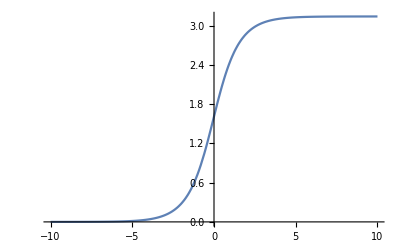

```mathematica
Plot[Evaluate[y[x]/.%],{x,-10,10}]
```

```mathematica
NDSolve[{y''[x]-Sin[2 y[x]]==0,y[-10]==0,y[10]==π},y,{x,-10,10}]
```

NDSolve::berr: The scaled boundary value residual error of 4619.41 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{y→InterpolatingFunction[{{-10., 10.}}, <>]}}

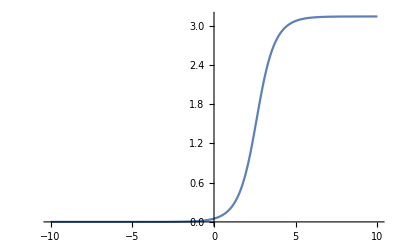

```mathematica
Plot[Evaluate[y[x]/.%],{x,-10,10}]
```

```mathematica
NDSolve[{y''[x]-1/2 Sin[2 y[x]]==0,y[-10]==0,y[10]==π,y'[-10]==0,y'[10]==0},y,{x,-10,10}]
```

NDSolve::nlnum1: The function value {0., -3.14159, 0., 0.} is not a list of numbers with dimensions {2} when the arguments are {0., 0., 0., 0.}.

NDSolve[{-1/2 Sin[2 y[x]]+y''[x]==0,y[-10]==0,y[10]==π,y'[-10]==0,y'[10]==0},y,{x,-10,10}]

```mathematica
FullSimplify[D[Log[Tan[θ/2]],θ],Assumptions->{θ∈Reals,θ<0,θ≤2 π}]
```

Csc[θ]

```mathematica
Tan[π/2]
```

ComplexInfinity